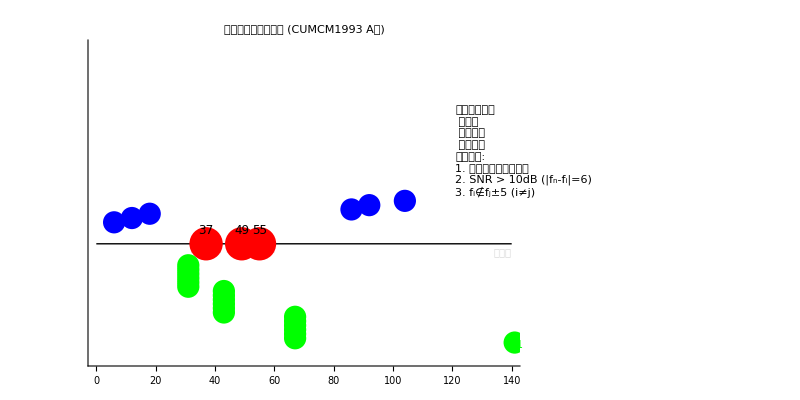

```mathematica
(*可更换为其他5组解*)
freq={37,49,55};
{f1,f2,f3}=freq;
secondOrder=Sort@{f1+f2,f1+f3,f2+f3,Abs[f1-f3],Abs[f1-f2],Abs[f2-f3]};
thirdOrder=Sort@{f1+f2+f3,Abs[f1+f2-f3],Abs[f1-f2+f3],Abs[f1-f2-f3],Abs[f2+f3-f1],Abs[f2-f3+f1],Abs[f2-f3-f1],Abs[f3+f1-f2],Abs[f3-f1+f2],Abs[f3-f1-f2],Abs[f2+f1-f3],Abs[f2-f1+f3],Abs[f2-f1-f3],Abs[f1+f3-f2],Abs[f1-f3+f2],Abs[f1-f3-f2],Abs[f3+f2-f1],Abs[f3-f2+f1],Abs[f3-f2-f1]};

(*动态计算图形高度*)
verticalRange={-0.4-Max[Length/@{secondOrder,thirdOrder}]/20,0.4+Max[Length/@{freq,secondOrder,thirdOrder}]/10};

Graphics[{{Black,Thick,Line[{{0,0},{140,0}}]},(*原频率：红色大圆点*){RGBColor[1,0,0],PointSize[0.03],Point[{#,0}&/@freq]},Text[Style[#,12],{#1,0.15}]&@@@Transpose[{freq,{"f₁=36","f₂=42","f₃=55"}}],(*二阶交调：蓝色圆点（垂直分布)*)MapIndexed[{RGBColor[0,0,1],PointSize[0.02],Point[{#1,0.2+#2[[1]]*0.05}],Text[Style[#1,10],{#1,0.2+#2[[1]]*0.05+0.03}]}&,secondOrder],(*三阶交调：绿色圆点（垂直分布)*)MapIndexed[{RGBColor[0,1,0],PointSize[0.02],Point[{#1,-0.2-#2[[1]]*0.05}],Text[Style[#1,10],{#1,-0.2-#2[[1]]*0.05-0.03}]}&,thirdOrder],(*接收带标注*){LightGray,Dashed,Line[{{#-5,-0.1},{#+5,-0.1}}]&/@freq,Text[Style["接收带",10],{140,-0.1},Right]},(*图例（右侧浮动布局)*)Inset[Column[{Style["频率成分图例",Bold],Row[{Graphics[{RGBColor[1,0,0],PointSize[0.03],Point[{0,0}]},ImageSize->20]," 原频率"}],Row[{Graphics[{RGBColor[0,0,1],PointSize[0.02],Point[{0,0}]},ImageSize->20]," 二阶交调"}],Row[{Graphics[{RGBColor[0,1,0],PointSize[0.02],Point[{0,0}]},ImageSize->20]," 三阶交调"}],Style["设计要求:",Bold],"1. 交调不得进入接收带","2. SNR > 10dB (|fₙ-fᵢ|=6)","3. fᵢ∉fⱼ±5 (i≠j)"},Alignment->Left,Spacing->0.5],Scaled[{0.85,0.8}],{Left,Top}]},Axes->{True,False},Ticks->{Range[0,140,10],None},PlotRange->{{0,140},verticalRange},ImageSize->{800,400},(*固定宽度，高度自适应*)AspectRatio->Full,(*取消固定宽高比*)PlotLabel->Style["非线性交调频率设计 (CUMCM1993 A题)",14,Bold],Background->White]
```